```mathematica
ClearAll["Global`*"]
L= 400;
F=800;
b=30;
h=20;
EE=210*10^3;
sigma = 450;
```

```mathematica
II=b*h^3/12;
```

```mathematica
alpha=F/(EE*II);
```

```mathematica
C1=(3/2)*alpha*L^2;
C2=(-4/3)*alpha*L^3
C3=2*alpha*L^2;
C4=(-3/2)*alpha*L^3;
C5=(13/2)*alpha*L^2;
C6=(-6)*alpha*L^3;
```

-1024/63

```mathematica
y1[x_]:=-x^3/6*alpha+C1*x+C2
y2[x_]:=-alpha*L*x^2/2+C3*x+C4
y3[x_]:=-alpha*(2*L*x^2-x^3/6)+C5*x+C6
```

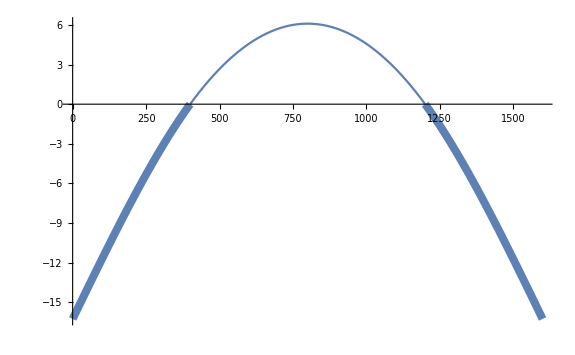

```mathematica
P1=Plot[y1[x],{x,0,L},PlotStyle->{Thickness[0.01]}];
P2=Plot[y2[x],{x,L,3L}];
P3=Plot[y3[x],{x,3L,4L},PlotStyle->{Thickness[0.01]}];
Show[P1,P2,P3,PlotRange->All]
```